```mathematica
sol = DSolve[{y''[x]+y[x]==0,y[0]==1,y'[0]==1/3},y,x]
```

{{y→Function[{x},1/3 (3 Cos[x]+Sin[x])]}}

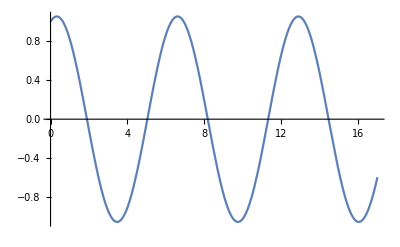

```mathematica
Plot[y[x]/.sol,{x,0,17}]
```

```mathematica
sol2 =DSolve[{y''[x]+y[x]==0,y[0]==1,y'[0]==1/3},y[x],x]
```

{{y[x]→1/3 (3 Cos[x]+Sin[x])}}

```mathematica
Plot[y[x]/.sol2,{x,0,17}]
```

-Graphics-

```mathematica
(*Метод Эйлера явный*)
```

```mathematica
EulerExpl[dy_,y0_,t0_,tlast_,h_ ]:=Module[{yPrev,yCurr,tPrev, list, n},
n = (tlast - t0)/h;
tPrev = t0;
list = {y0};
Do[yPrev = Last[list];
yCurr = yPrev+dy[tPrev,yPrev]*h;

tPrev = tPrev+h;
AppendTo[list, yCurr], {i, 1, n}];Return[list]]
```

```mathematica
(*Обобщенный метод Эйлера*)
```

```mathematica
EulerGen[dy_,y0_,t0_,tlast_,h_ ]:=Module[{ynewPrev,yPrev,ynewCurr,yCurr,tPrev, listY, n},
n = (tlast - t0)/h;
tPrev = t0;
listY = {y0};
Do[
yPrev = Last[listY];
ynewCurr = yPrev + dy[tPrev,yPrev]*h;
yCurr = yPrev+(dy[tPrev,yPrev]+dy[tPrev+h,ynewCurr])*h/2;

tPrev = tPrev+h;
AppendTo[listY, yCurr], {i, 1, n}];Return[listY]]
```

```mathematica
(*функция которая считает все списки и выводит график явного, обобщенного метода Эйлера и аналитический график*)
```

```mathematica
DoEulers[dy_,y0_,t0_,tlast_,h_, answers_]:=Module[{solv,y,tPrev,t1,listGen,listE, listGenPoints,listEPoints, listT,listDiffE,listDiffGen,listDiffPointsE,listDiffPointsGen},
solv = DSolve[{y'[t1]==dy,y[0]==1},y[t1],{t1,0,1}];
listE = EulerExpl[dy, y0, t0, tlast, h];
listT = {t0};
Do[tPrev = Last[listT];

AppendTo[listT, tPrev+h], {i, 1, Length[listE]}];
listGen =EulerGen[dy, y0, t0, tlast, h] ;

listGenPoints =  Partition[Riffle[listT,listGen],2];
listEPoints = Partition[Riffle[listT,listE],2];
listDiffE = answers- listE;
listDiffGen = answers- listGen;
listDiffPointsE = Partition[Riffle[listT,listDiffE],2];
listDiffPointsGen = Partition[Riffle[listT,listDiffGen],2];
plot1 = ListPlot[listEPoints];
plot2 = ListPlot[listGenPoints, PlotStyle->Green];
plot3 = ListPlot[listDiffPointsGen, PlotStyle->Green];
plot4 = ListPlot[listDiffPointsE];
Return[{plot1, plot2,plot3,plot4}]

]
```

```mathematica
(*Задание 1*)
```

```mathematica
func1[t1_,y1_] := 2*t1+0*y1;
```

```mathematica
solv1 = DSolve[{y1'[t1]==2t1,y1[0]==1},y1[t1],{t1,0,1}]
```

{{y1[t1]→1+t1^2}}

```mathematica
(*h = 0.1*)
```

```mathematica
list11an=Flatten[y1[t1]/.solv1/.t1->Range[0,1,0.1]]
```

{1.,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2.}

```mathematica
plots11 = DoEulers[func1, 1, 0, 1, 0.1, list11an];
```

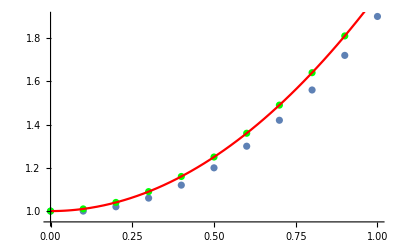

```mathematica
Show[plots11[[1]],plots11[[2]], Plot[y1[t1]/.solv1,{t1,0,1},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

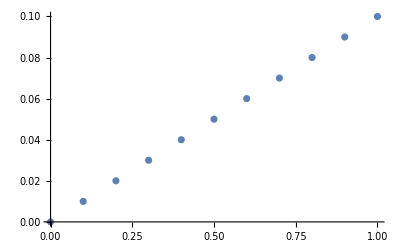

```mathematica
Show[plots11[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

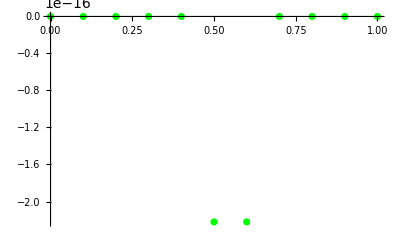

```mathematica
Show[plots11[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

```mathematica
(*для h = 0.1: обобщенный метод Эйлера визуально совпадает с аналитическим решением (почти постоянная (с странными скачками) очень маленькая погрешность), в явном методе погрешность растет*)
```

```mathematica
(*h = 0.05*)
```

```mathematica
list12an=Flatten[y1[t1]/.solv1/.t1->Range[0,1,0.05]];
```

```mathematica
plots12 = DoEulers[func1, 1, 0, 1, 0.05, list12an];
```

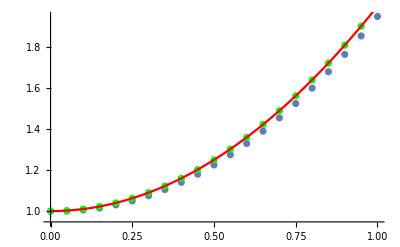

```mathematica
Show[plots12[[1]],plots12[[2]], Plot[y1[t1]/.solv1,{t1,0,1},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

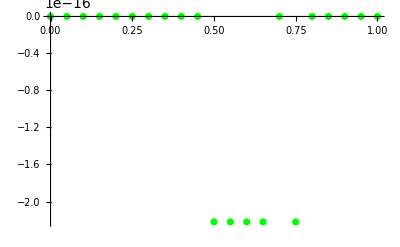

```mathematica
Show[plots12[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

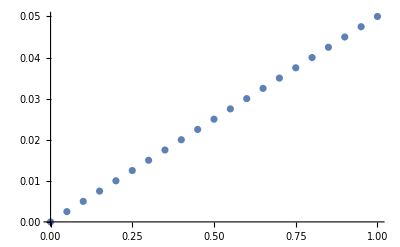

```mathematica
Show[plots12[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.05: обобщенный метод Эйлера почти совпадает с аналитическим решением (ошибка иногда скачет, но очень мала), ошибка явного метода растет*)
```

```mathematica
(*h = 0.05*)
```

```mathematica
list13an=Flatten[y1[t1]/.solv1/.t1->Range[0,1,0.01]];
```

```mathematica
plots13 = DoEulers[func1, 1, 0, 1, 0.01, list13an];
```

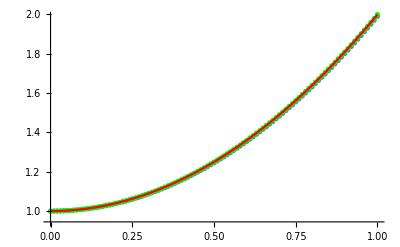

```mathematica
Show[plots13[[1]],plots13[[2]], Plot[y1[t1]/.solv1,{t1,0,1},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

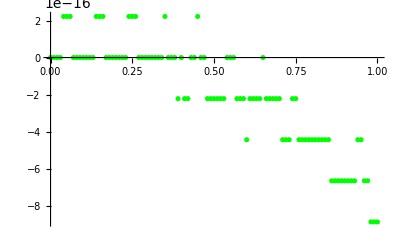

```mathematica
Show[plots13[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

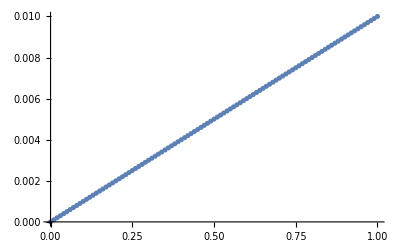

```mathematica
Show[plots13[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.01: оба метода Эйлера очень хорошо приближают значение к аналитическому, ошибка обобщенного метода меняется странно (растет по модулю ступенчато), явного - растет*)
```

```mathematica
(*Задание 2*)
```

```mathematica
func2[t2_,y2_]:=6t2^2
```

```mathematica
solv2 = DSolve[{y2'[t2]==6t2^2,y2[0]==1},y2[t2],{t2,0,2}]
```

{{y2[t2]→1+2 t2^3}}

```mathematica
(*h = 0.1*)
```

```mathematica
list21an=Flatten[y2[t2]/.solv2/.t2->Range[0,2,0.1]];
```

```mathematica
plots21= DoEulers[func2, 1, 0, 2, 0.1, list21an];
```

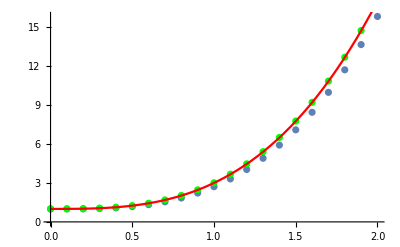

```mathematica
Show[plots21[[1]],plots21[[2]], Plot[y2[t2]/.solv2,{t2,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

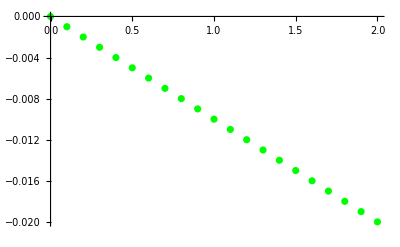

```mathematica
Show[plots21[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

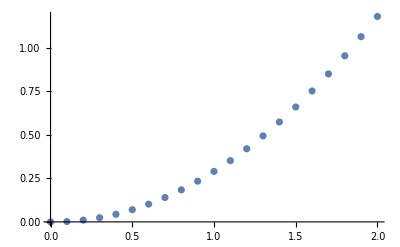

```mathematica
Show[plots21[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.1: обобщенный метод Эйлера приближает лучше, погрешность обобщенного метода растет также как раньше росла погрешность явного? растет линейно, в то же время погрешность явного растет быстрее линейной*)
```

```mathematica
(*h = 0.05*)
```

```mathematica
list22an=Flatten[y2[t2]/.solv2/.t2->Range[0,2,0.05]];
```

```mathematica
plots22= DoEulers[func2, 1, 0, 2, 0.05, list22an];
```

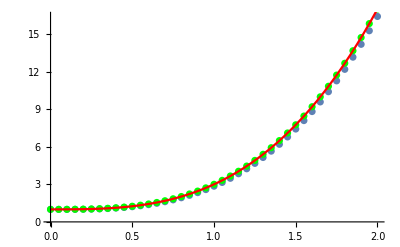

```mathematica
Show[plots22[[1]],plots22[[2]], Plot[y2[t2]/.solv2,{t2,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

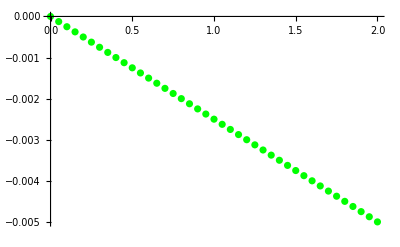

```mathematica
Show[plots22[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

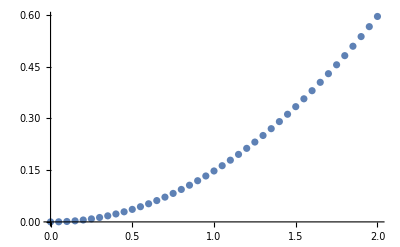

```mathematica
Show[plots22[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.05: оба метода довольно хорошо приближают,погрешность обобщенного метода растет линейно, погрешность явного растет быстрее линейной, и погрешность явного метода всегда больше*)
```

```mathematica
(*h = 0.01*)
```

```mathematica
list23an=Flatten[y2[t2]/.solv2/.t2->Range[0,2,0.01]];
```

```mathematica
plots23= DoEulers[func2, 1, 0, 2, 0.01, list23an];
```

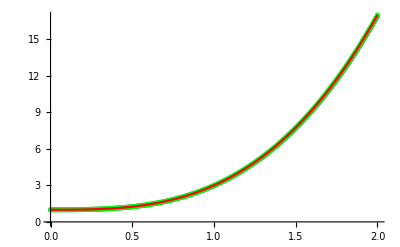

```mathematica
Show[plots23[[1]],plots23[[2]], Plot[y2[t2]/.solv2,{t2,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

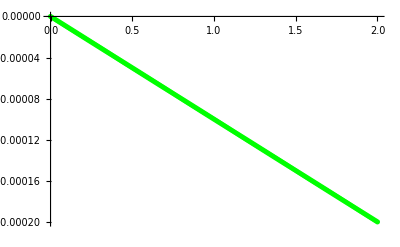

```mathematica
Show[plots23[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

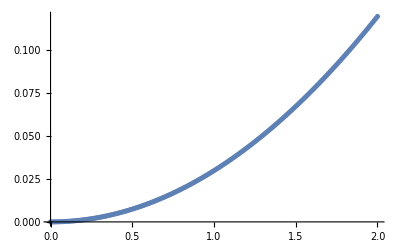

```mathematica
Show[plots23[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.01: оба метода хорошо приближают, погрешности как раньше, погрешность явного метода намного больше*)
```

```mathematica
(*Задание 3*)
```

```mathematica
func3[y3_,t3_]:=2*y3*t3
```

```mathematica
solv3 = DSolve[{y3'[t3]==2*y3[t3]*t3,y3[0]==1},y3[t3],{t3,0,2}]
```

{{y3[t3]→ⅇ^(t3^2)}}

```mathematica
(*h = 0.1*)
```

```mathematica
list31an=Flatten[y3[t3]/.solv3/.t3->Range[0,2,0.1]];
```

```mathematica
plots31= DoEulers[func3, 1, 0, 2, 0.1, list31an];
```

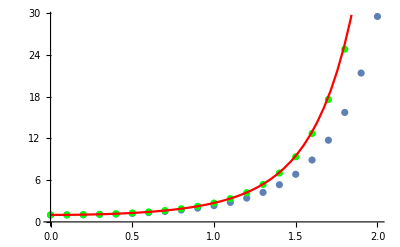

```mathematica
Show[plots31[[1]],plots31[[2]], Plot[y3[t3]/.solv3,{t3,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

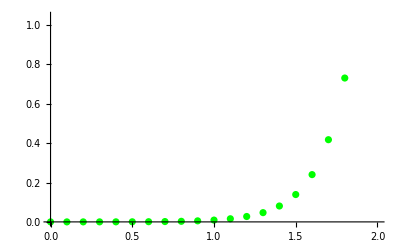

```mathematica
Show[plots31[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

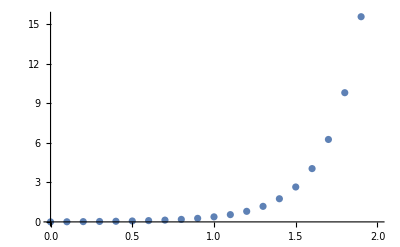

```mathematica
Show[plots31[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.1: обобщенный метод приближает лучше, ошибка растет экспоненциально? и в том, и в другом случае, ошибка явного метода в разы больше*)
```

```mathematica
(*h = 0.05*)
```

```mathematica
list32an=Flatten[y3[t3]/.solv3/.t3->Range[0,2,0.05]];
```

```mathematica
plots32= DoEulers[func3, 1, 0, 2, 0.05, list32an];
```

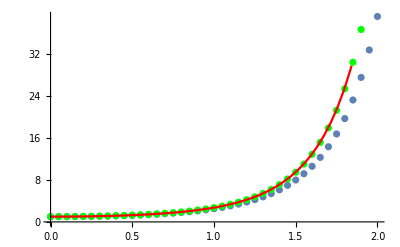

```mathematica
Show[plots32[[1]],plots32[[2]], Plot[y3[t3]/.solv3,{t3,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

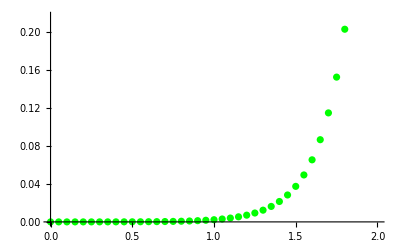

```mathematica
Show[plots32[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

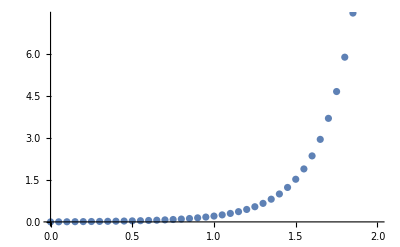

```mathematica
Show[plots32[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.05: все так же, только разбиение чаще*)
```

```mathematica
(*h = 0.01*)
```

```mathematica
list33an=Flatten[y3[t3]/.solv3/.t3->Range[0,2,0.01]];
```

```mathematica
plots33= DoEulers[func3, 1, 0, 2, 0.01, list33an];
```

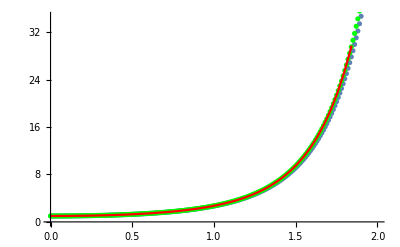

```mathematica
Show[plots33[[1]],plots33[[2]], Plot[y3[t3]/.solv3,{t3,0,2},PlotStyle->Red]]
```

```mathematica
(*Аналитическое решение, явный (синим) и обобщенный(зеленым) Эйлеры*)
```

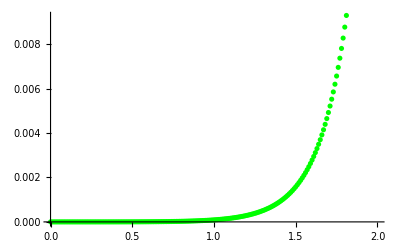

```mathematica
Show[plots33[[3]]]
```

```mathematica
(*Погрешность для обобщенного метода Эйлера*)
```

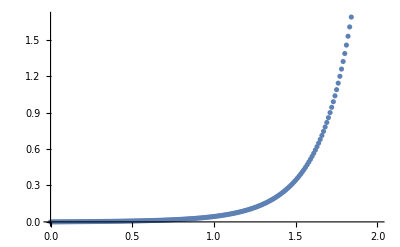

```mathematica
Show[plots33[[4]]]
```

```mathematica
(*Погрешность для явного метода Эйлера*)
```

```mathematica
(*для h = 0.01: оба метода приближают хорошо, погрешность растет как раньше, погрешность явного метода больше*)
```